# Project report

## Temperature control: set points and times.

D Malan

Department of Chemistry
University of Pretoria

12 February 2020

## Introduction

In yesterday’s report the impact of imprecise control on the chromatography was discussed. From the data it seems that small changes to the temperature ramp can lead to unfortunate peak shifts in the chromatograms. These changes were attributed to inaccurate control by the PID, due to approximations in the algorithm and a non-deterministic operating system.

However, further investigation showed that not only the control is imprecise, the temperature set points are also not precise. This means that the temperature ramps are also not repeatable.

## Experimental

Data from a previous SFC×GC run was examined: 2020_02_11-120014.dat

## Calculations

A typical comparison graph looks like this.

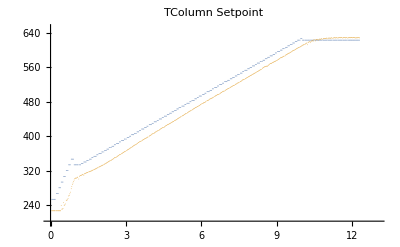

## Results

The results show that the measured temperature follows the set point quite well. It is differences between the set point ramps that lead to different temperature ramps for consecutive GC runs, rather than problems with controlling the temperature.

For two consecutive fast GC runs (90 and 91), the times at which the temperature programs pass 500 °C are 6.66 s and 6.73 s respectively. This is difference of 70 ms, and is associated with a peak shift at r_t= 9.6 of 100 ms, which is just about equal to the peak width of 108 ms.

## Discussion

The measured temperature followed the setpoint quite well. Of course the temperature was always lower than the setpoint, because the ramp never allowed the temperature to increase above the set point, so the integral term of the PID controller could never become zero.

The stepwise change in the set point is expected. The loop in the software that controls the power to the coaxial heater runs every 200 ms, but the data collection loop takes between 15 and 60 milliseconds, depending on how busy the computer is. So data points are collected more frequently than the set point is updated. The inertia of the system

At around 1 s in the graph above there is an unexpected hump in the set point. This is not how the set point is supposed to change. The same thing happens at the end of the ramp, just before the hold at the top temperature. After the hump the set point seems to be constant for two or three control periods. Similarly, the set point at the start of the temperature program seems to be constant for an extra one or two control periods, which does not help with getting the temperature rising. In other fast GC runs a similar stationary point in the setpoint can be seen, even if there is no “hump”:
-Graphics-

Examination of the code revealed that the concept of time is poorly defined. At various points in the program a time record is created by reading the millisecond timer library VI. Although time is recorded in the data file, it is not clear how this time relates to the time the data was recorded. The best one can say is that the time in the data record was between the time the buffer was read and the time the data was recorded. This is a short time, and experience shows that it is a fairly repeatable time, but it’s still ill-defined.

Gradient times run to their own clock again.

In yesterday’s report cryogen bleeding was blamed for the slow start of the temperature program. This might be true, but an additional factor plays a role: the Integral term of the PID controller is reset to zero at the start of the temperature program. This is reasonable, because the cooling period is variable and causes a variable integral term to be present at the start of the temperature program, which causes variable temperature programs. In fact, I remember realizing the need for the integral term reset and was impressed by the improvement it brought. However, because the integral term is small at the start of the temperature program, the power demand is low, so the heating is delayed. A possible hack for this problem is to increase the set point at the start of the temperature program. This will increase the P-term, which will demand more power and so lead to a faster start of the temperature rising, and will also help to increase the I-term faster. Of course none of these will make much of a difference if the

## Conclusion

The variability of the temperature program between GC runs is primarily determined by the difference between the temperature set point ramps, and only to a lesser extent by the use of a non-deterministic operating system.

## Recommendations

Examine the algorithm that generates the gradients and identify the problem with stationary points.

Harmonize the use of time throughout the control software.

Use real-time operating systems with deterministic timing when building scientific instruments.

Increase the setpoint at the start of the temperature ramp.